## percentages

### one case

```mathematica
zeroFields={};
mLs={};
xmins={};
Vmins={};
seeds={};
mLnBFB={};

Table[
datapath=NotebookDirectory[]<>"percentage-data/posall-abfix/result"<>ToString[i]<>".h5";
zeroFields=Join[zeroFields,Import[datapath,"zerofields"]];
mLs=Join[mLs,Import[datapath,"m_L"]];
xmins=Join[xmins,Import[datapath,"x_min"]];
Vmins=Join[Vmins,Import[datapath,"V_min"]];
seeds=Join[seeds,Import[datapath,"seed"]];

,{i,100(*{""}*)}];

Print[Length[Vmins]]
Dynamic[ishow]
```

2100

```mathematica
same[x1_,x2_,ϵ_:10^-4]:=Abs[(Abs[x1]-Abs[x2])]<ϵ

badDueToA[xmin_]:=same[Table[xmin⟦j⟧,{j,1,2}]//Abs//Max,0];
badDueToB[xmin_]:=same[Table[xmin⟦j⟧,{j,3,8}]//Abs//Max,0];
badDueToC[xmin_]:=Not[same[det2[xmin]//Abs//Max,0]];
(*badDueToD[xmin_]:=And[same[xmin⟦3⟧,xmin⟦6⟧],same[xmin⟦4⟧,xmin⟦7⟧],same[xmin⟦5⟧,xmin⟦8⟧]];*)
badDueToD[xmin_]:=same[xmin⟦3⟧^2+2 xmin⟦4⟧^2+xmin⟦5⟧^2,xmin⟦6⟧^2+2 xmin⟦7⟧^2+xmin⟦8⟧^2];
goodE[xmin_]:=Or[same[xmin⟦1⟧,xmin⟦2⟧,10^-2],same[xmin⟦3⟧xmin⟦5⟧,0]&&same[xmin⟦4⟧,0]&&same[xmin⟦6⟧xmin⟦8⟧,0]&&same[xmin⟦7⟧,0]];

type=Table[0,{i,Length[zeroFields]}];
Do[

If[badDueToA[xmins⟦i⟧],
type⟦i⟧="A";Continue[]
];
If[badDueToB[xmins⟦i⟧],
type⟦i⟧="B";Continue[]
];
If[badDueToC[xmins⟦i⟧],
type⟦i⟧="C";Continue[]
];
If[badDueToD[xmins⟦i⟧],
type⟦i⟧="D";Continue[]
];

If[goodE[xmins⟦i⟧],
type⟦i⟧="E";Continue[]
];

type⟦i⟧="X:unknown";

ishow=i;
,{i,Length[zeroFields]}];

tallyList=type//Tally

Print[SortBy[%,First],
Length[seeds]
]
EandAll={Select[tallyList,#⟦1⟧=="E"&]⟦1,2⟧,Length[seeds]}
1.0EandAll⟦1⟧/EandAll⟦2⟧
```

{{B,501},{D,273},{E,329},{C,754},{A,231},{X:unknown,12}}

{{A,231},{B,501},{C,754},{D,273},{E,329},{X:unknown,12}}2100

{329,2100}

0.156667

### 1+2 cases - automatic

```mathematica
Table[
zeroFields={};
mLs={};
xmins={};
Vmins={};
seeds={};
mLnBFB={};

Table[
datapath=If[case=="all",NotebookDirectory[]<>"percentage-data/all/result-gen"<>ToString[i]<>".h5",
NotebookDirectory[]<>"percentage-data/"<>case<>"/result"<>ToString[i]<>".h5"];
zeroFields=Join[zeroFields,Import[datapath,"zerofields"]];
mLs=Join[mLs,Import[datapath,"m_L"]];
xmins=Join[xmins,Import[datapath,"x_min"]];
Vmins=Join[Vmins,Import[datapath,"V_min"]];
seeds=Join[seeds,Import[datapath,"seed"]];

,{i,If[case=="all",100,100]}];


type=Table[0,{i,Length[zeroFields]}];
Do[

If[badDueToA[xmins⟦i⟧],
type⟦i⟧="A";Continue[]
];
If[badDueToB[xmins⟦i⟧],
type⟦i⟧="B";Continue[]
];
If[badDueToC[xmins⟦i⟧],
type⟦i⟧="C";Continue[]
];
If[badDueToD[xmins⟦i⟧],
type⟦i⟧="D";Continue[]
];

If[goodE[xmins⟦i⟧],
type⟦i⟧="E";Continue[]
];

type⟦i⟧="X:unknown";

ishow=i;
,{i,Length[zeroFields]}];

tallyList=SortBy[type//Tally,First];

EandAll={Select[tallyList,#⟦1⟧=="E"&]⟦1,2⟧,Length[seeds]};
Print[tallyList,"\n", tallyList⟦All,2⟧];
Print[EandAll,1.0EandAll⟦1⟧/EandAll⟦2⟧];

,{case,{"all","posall-abfix","strong-constraints"}}]
```

{{A,70380},{B,70625},{C,683},{D,3135},{E,68}}
{70380,70625,683,3135,68}

{68,144891}0.000469318

{{A,231},{B,501},{C,754},{D,273},{E,329},{X:unknown,12}}
{231,501,754,273,329,12}

{329,2100}0.156667

{{A,85},{B,258},{C,3},{D,1},{E,2069},{X:unknown,49}}
{85,258,3,1,2069,49}

{2069,2465}0.839351

{Null,Null,Null}

X (also C, D when they are small) have been inspected by another program and it turns out that 
[231, 501, 754, 273, 329 + 12]
[85, 258 + 1, 0, 0, 2069 + 49 + 3]

## For α123β123 plots

```mathematica
xstr={"m1q","m2q","m3q",
"L1","L2","L3","L4",
"r1","r2","r3","r4",
"a1","a2","a3",
"b1","b2","b3"};
xid=Association[Table[xstr⟦i⟧->i,{i,xstr//Length}]];

centralmodel=1.0{5.0,2.0,9.0,
1.0,0.0,1.2,0.0,
1.0,0.2,3.0,0.0,
0.5,0,0.7,
0,0,0};

xlist=1.0Subdivide[-4π,4π,39];
ylist=1.0Subdivide[-4π,4π,39];
labelPairs={{"a1","a2"},{"a2","a3"},{"a3","a1"},{"b1","b2"},{"b2","b3"},{"b3","b1"}};

mLs={};
Table[
mLs=Join[mLs,
Table[model0=centralmodel;
model0⟦xid⟦label⟦1⟧⟧⟧=x;
model0⟦xid⟦label⟦2⟧⟧⟧=y;
model0
,{x,xlist},{y,ylist}]//Flatten[#,1]&
];
,{label,labelPairs}];
Print[{"mLs size",mLs//Dimensions}];
```

{mLs size,{9600,17}}

```mathematica
(*do not run them again!!!*)
nkernal=100;
If[Mod[Length[mLs],nkernal]==0,Print["OK"],Interrupt[]];
mLss=Partition[mLs,Length[mLs]/nkernal];
Table[Export[NotebookDirectory[]<>"scan-a123b123-data/input"<>ToString[i]<>".h5",{"mLs"-> mLss⟦i⟧}],{i,Length[mLss]}];
```

OK

```mathematica
(*************)
(*************)

(**run python:*)
(*
command=Table[" python compute-a123b123.py "<>ToString[i]<>" & ",{i,1,nkernal}]//StringJoin
**)
(*copy the result as "plain text"*)
(*************)
(*running time, ~120min*)
```

```mathematica
(*import python result*)
zeroFields={};
mLs={};
xmins={};
Vmins={};
seeds={};
mLnBFB={};

Table[
datapath=NotebookDirectory[]<>"scan-a123b123-data/result"<>ToString[i]<>".h5";
If[FileExistsQ[datapath],
zeroFields=Join[zeroFields,Import[datapath,"zerofields"]];
mLs=Join[mLs,Import[datapath,"m_L"]];
xmins=Join[xmins,Import[datapath,"x_min"]];
Vmins=Join[Vmins,Import[datapath,"V_min"]];
seeds=Join[seeds,Import[datapath,"seed"]];
mLnBFB=Join[mLnBFB,Import[datapath,"m_L_nBFB"]];
,
Print["not exist:"<>datapath];
];

,{i,nkernal(*{""}*)}];

Print[Length[Vmins]]
Dynamic[ishow]
```

1620

```mathematica
same[x1_,x2_,ϵ_:10^-4]:=Abs[(Abs[x1]-Abs[x2])]<ϵ

badDueToA[xmin_]:=same[Table[xmin⟦j⟧,{j,1,2}]//Abs//Max,0];
badDueToB[xmin_]:=same[Table[xmin⟦j⟧,{j,3,8}]//Abs//Max,0];
badDueToC[xmin_]:=Not[same[det2[xmin]//Abs//Max,0]];
(*badDueToD[xmin_]:=And[same[xmin⟦3⟧,xmin⟦6⟧],same[xmin⟦4⟧,xmin⟦7⟧],same[xmin⟦5⟧,xmin⟦8⟧]];*)
badDueToD[xmin_]:=same[xmin⟦3⟧^2+2 xmin⟦4⟧^2+xmin⟦5⟧^2,xmin⟦6⟧^2+2 xmin⟦7⟧^2+xmin⟦8⟧^2];
goodE[xmin_]:=Or[same[xmin⟦1⟧,xmin⟦2⟧,10^-2],same[xmin⟦3⟧xmin⟦5⟧,0]&&same[xmin⟦4⟧,0]&&same[xmin⟦6⟧xmin⟦8⟧,0]&&same[xmin⟦7⟧,0]];

type=Table[0,{i,Length[zeroFields]}];
Do[
ishow=i;
If[badDueToA[xmins⟦i⟧],
type⟦i⟧="A";Continue[]
];
If[badDueToB[xmins⟦i⟧],
type⟦i⟧="B";Continue[]
];
If[badDueToC[xmins⟦i⟧],
type⟦i⟧="C";Continue[]
];
If[badDueToD[xmins⟦i⟧],
type⟦i⟧="D";Continue[]
];

If[goodE[xmins⟦i⟧],
type⟦i⟧="E";Continue[]
];

type⟦i⟧="X:unknown";


,{i,Length[zeroFields]}];

tallyList=type//Tally

Print[SortBy[%,First],
Length[seeds]
]
EandAll={Select[tallyList,#⟦1⟧=="E"&]⟦1,2⟧,Length[seeds]}
1.0EandAll⟦1⟧/EandAll⟦2⟧
```

{{E,556},{A,709},{X:unknown,1},{C,91},{D,263}}

{{A,709},{C,91},{D,263},{E,556},{X:unknown,1}}1620

{556,1620}

0.34321

```mathematica
(**********************)
(*preparing for plots *)
(**********************)

δx=xlist⟦2⟧-xlist⟦1⟧;
δy=ylist⟦2⟧-ylist⟦1⟧;
plotgrid[xlist0_,ylist0_]:=Module[{xlist,ylist},

xlist=Append[xlist0-δx/2,xlist0⟦-1⟧+δx/2];

ylist=Append[ylist0-δy/2,ylist0⟦-1⟧+δy/2];
gridx=Table[Line[{{x,Min[ylist]},{x,Max[ylist]}}],{x,xlist}];
gridy=Table[Line[{{Min[xlist],y},{Max[xlist],y}}],{y,ylist}];
Graphics[{Gray,gridx,gridy}]
]
plotsamples[points_,color_]:=Graphics[{color,Table[Rectangle[point-{δx/2,δy/2},point+{δx/2,δy/2}],{point,points}]}]
```

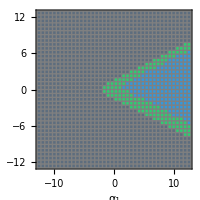
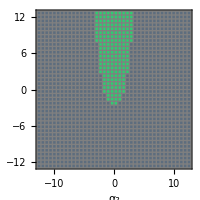
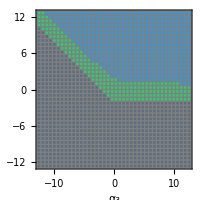
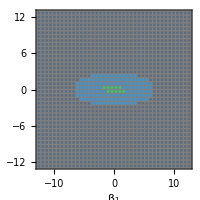
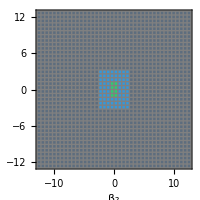
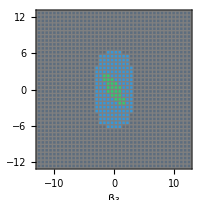

```mathematica
type2=type;
Do[type2⟦i⟧="E",{i,{130}}];
Do[type2⟦i⟧="E",{i,{426,447,422,420}}];

labelαβ={"a1"->"α_1","a2"->"α_2","a3"->"α_3","b1"->"β_1","b2"->"β_2","b3"->"β_3"};
plots=Table[
xlabel=label⟦1⟧;
ylabel=label⟦2⟧;
otherId=Delete[Range[Length[xstr]],{{xid[xlabel]},{xid[ylabel]}}];
positionE=Position[type2,"E"]//Flatten;
positionE=Select[positionE,(Abs[mLs⟦#,otherId⟧-centralmodel⟦otherId⟧]//Max)<10^-6&];
pointE=Table[{mLs⟦pos,xid[xlabel]⟧,mLs⟦pos,xid[ylabel]⟧},{pos,positionE}];
plotE=plotsamples[pointE,RGBColor["#2ECC71"]];
positionA=Position[type2,_?(MemberQ[{"A","B","C","D"},#]&)]//Flatten;
positionA=Select[positionA,(Abs[mLs⟦#,otherId⟧-centralmodel⟦otherId⟧]//Max)<10^-6&];
pointA=Table[{mLs⟦pos,xid[xlabel]⟧,mLs⟦pos,xid[ylabel]⟧},{pos,positionA}];
plotA=plotsamples[pointA,RGBColor["#3498DB"]];

mLnBFB0=Select[mLnBFB,(Abs[#⟦otherId⟧-centralmodel⟦otherId⟧]//Max)<10^-6&];

pointnBFB=Table[{mLnBFB0⟦pos,xid[xlabel]⟧,mLnBFB0⟦pos,xid[ylabel]⟧},{pos,Length[mLnBFB0]}];
plotnBFB=plotsamples[pointnBFB,RGBColor["#5D6D7E"]];

plot=Show[{plotE,plotA,plotnBFB,plotgrid[xlist,ylist]},PlotRange->{4π{-1,1},4π{-1,1}},
(*PlotRangeClipping->True,*)
PlotRangePadding->1.2{1,1},
Frame->True,Axes->False,ImageSize->200,FrameLabel->({xlabel,ylabel}/.labelαβ),AspectRatio->1];
(*Export["D:\\Dropbox\\mywork\\LR-scalar\\LR-V\\fig\\"<>xlabel<>ylabel<>".pdf",plot];*)
plot
,{label,labelPairs}
]
```

### Strange Samples Analysis

see data - analysis - v7.nb

### corresponding mass distributions

```mathematica
(*Table[{mLs⟦pos⟧},{pos,positionE}]*)
```

```mathematica
(*"m1q","m2q","m3q",
"L1","L2","L3","L4",
"r1","r2","r3","r4",
"a1","a2","a3",
"b1","b2","b3"*)
```

```mathematica
(*page 17*){"M11"->vR^2(-2r1+r3+4r2 r^2+a3 (1-ξ^2)ϵ^2+(8a2 ξ ϵ^2 sα sδ2)/(1-r^2)),"M22"->vR^2(4r2+(r3-2r1)r^2+a3 (1-ξ^2)ϵ^2+(8a2 r^2 ξ ϵ^2 sα sδ2)/(1-r^2)),
"M12"->vR^2(4r4 r Exp[-ⅈ θL]+(b1 Exp[-ⅈ α]+b2 ξ Exp[-2 ⅈ α])ξ ϵ^2+b3 ϵ^2)
}/.{
ξ->k2/k1(*=tanβ page 6*),ϵ->k1/vR(*page 6*),
r->vL/vR(*page 6*),sα->Sin[α],sδ2->Sin[δ2]}/.{δ2->0(*phase of α2*)}(*α, θL are phases of VEVs*)/.{k1->myk1/(√2),k2->myk2/(√2)}
```

```mathematica
(*ϕ=DiagonalMatrix[{κ1,κ2 Exp[i t2]}/√2];
ϕt=-ϵ.ϕ.ϵ/.cRep;
ΔL=({{x2, x3}, {x1, -x2}})/.{x1->x1 Exp[i f1],x2->x2 Exp[i f2],x3->x3 Exp[i f3]};
ΔR=({{y2, y3}, {y1, -y2}})/.{y1->y1 Exp[i g1],y2->y2 Exp[i g2],y3->y3 Exp[i g3]};*)
```

```mathematica
(*{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}*)
(*{θL->f1?g1,α->t2,vL->x1,myk1->k1,myk2->k2}*)
```

```mathematica
massfromλ[λ_(*potential para*),xmin_(*xmin*)]:=(*normalized v scale to 246GeV*)Module[{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3,(**)
m1q,m2q,m3q,L1,L2,L3,L4,r1,r2,r3,r4,a1,a2,a3,b1,b2,b3,(**)
vevRep,
other
},
{m1q,m2q,m3q,L1,L2,L3,L4,r1,r2,r3,r4,a1,a2,a3,b1,b2,b3}=λ;
{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}=canonicalize[xmin];


vevRep={(*Print[{f1,g1}];*)θL->f1-g1(*Warning: what if g1 are nonzero*),α->t2,vL->x1,vR->y1,myk1->k1,myk2->k2};

{"M11"->(-2 r1+r3+(a3 myk1^2 (1-myk2^2/myk1^2))/(2 vR^2)+(4 r2 vL^2)/vR^2) vR^2,"M22"->(4 r2+(a3 myk1^2 (1-myk2^2/myk1^2))/(2 vR^2)+((-2 r1+r3) vL^2)/vR^2) vR^2,"M12"->((b3 myk1^2)/(2 vR^2)+(myk1 myk2 (b1 ⅇ^(-ⅈ α)+(b2 ⅇ^(-2 ⅈ α) myk2)/myk1))/(2 vR^2)+(4 ⅇ^(-ⅈ θL) r4 vL)/vR) vR^2,"246GeV"->√(k1^2+k2^2)(*246.0/(√2)=173.xxx*)}/.vevRep]
```

```mathematica
iσ2=ⅈ PauliMatrix[2];
iσ2.({{x2, x3}, {x1, -x2}}).iσ2†
({{x2, x3}, {x1, -x2}})/.{x2->-x2,x1->-x3,x3->-x1}
(*y same, UL=UR*)
iσ2.({{k1, 0}, {0, k2}}).iσ2†
```

{{-x2,-x1},{-x3,x2}}

{{-x2,-x1},{-x3,x2}}

{{k2,0},{0,k1}}

```mathematica
maxabs[x_]:=Max[Abs[x]];

iσ2Transform[x_]:=Module[{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3},{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}=x;
{k2,k1,-x3,-x2,-x1,-y3,-y2,-y1,t2+0,f3,f2,f1,g3,g2,g1}
]

parityTransform[x_]:=Module[{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3},{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}=x;
{k1,k2,y1,y2,y3,x1,x2,x3,-t2,g1,g2,g3,f1,f2,f3}
]



canonicalize[xmin_]:=Module[{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3,(**)
exchange123,temp},
{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}=xmin;
If[maxabs[{x1,x2,x3}]>maxabs[{y1,y2,y3}],
(*exchange123={x1,x2,x3};{x1,x2,x3}={y1,y2,y3};{y1,y2,y3}=exchange123;
t2=-t2;*)
{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}=parityTransform[xmin]
];
(*If[Abs[x1]<Abs[x3],temp=x1;x1=x3;x3=temp];
If[Abs[y1]<Abs[y3],temp=y1;y1=y3;y3=temp];*)
If[Abs[y1]<Abs[y3],{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}=iσ2Transform[{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}]
];


If[x1<0,x1=-x1;f1=f1+π];
If[y1<0,y1=-y1;g1=g1+π];
If[k1<0,k1=-k1;t2=t2+π];
If[k2<0,k2=-k2;t2=t2+π];
(*If[same[Vatx[mλ,xmin],
Vatx[mλ,xmin//canonicalize]],Interrupt[]]*)
If[Or[k1<0,k2<0,x1<0,y1<0,Abs[x2]>0.1,Abs[x3]>0.1,Abs[y2]>0.1,Abs[y3]>0.1],Print[posOutput,{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}];(*Interrupt[]*)];
{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}
]
```

```mathematica
Clear[m1q,m2q,m3q,L1,L2,L3,L4,r1,r2,r3,r4,a1,a2,a3,b1,b2,b3]
```

```mathematica
(*Table[xmins⟦pos⟧,{pos,positionE}]*)
```

```mathematica
massMatrix[rule_]:=(*x^2*)((*x->*)(246(*GeV*))/("246GeV"))^2{{"M11","M12"},{"M12","M22"}}/.rule
```

```mathematica
positionE=Position[type,"E"]//Flatten;
(*positionE=Position[type2,"E"]//Flatten*)

Table[mLs⟦pos⟧,{pos,positionE⟦3;;3⟧}]
Table[xmins⟦pos⟧,{pos,positionE⟦3;;3⟧}]
Table[xmins⟦pos⟧//canonicalize,{pos,positionE⟦3;;3⟧}]
```

{{5.,2.,9.,1.,0.,1.2,0.,1.,0.2,3.,0.,-0.966644,-0.966644,0.7,0.,0.,0.}}

{{-6.27367,-3.53218,-3.40809×10^-8,-6.90402×10^-10,-5.18674×10^-8,6.02194,-1.25063×10^-8,-2.74317×10^-9,-8.64805×10^-9,-2.47416,1.46476,-4.66805,-0.0981321,1.10841,-0.955694}}

{{6.27367,3.53218,3.40809×10^-8,-6.90402×10^-10,-5.18674×10^-8,6.02194,-1.25063×10^-8,-2.74317×10^-9,6.28319,0.667435,1.46476,-4.66805,-0.0981321,1.10841,-0.955694}}

```mathematica
Table[massfromλ[mLs⟦pos⟧,xmins⟦pos⟧//canonicalize],{pos,positionE⟦3;;3⟧}]
```

{{M11→45.6727,M22→38.42,M12→0.,246GeV→7.19967}}

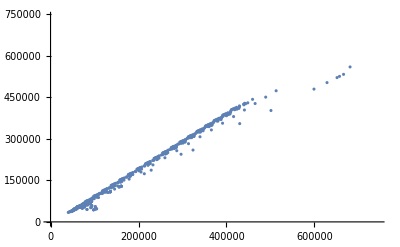

```mathematica
(*Table[massfromλ[mLs⟦pos⟧,xmins⟦pos⟧],{pos,positionE}]*)
Table[massfromλ[mLs⟦pos⟧,xmins⟦pos⟧//canonicalize]//massMatrix//Re//Eigenvalues,{pos,positionE}]//ListPlot
```

```mathematica
(*plotsamples[pointE,RGBColor["#2ECC71"]]*)
```

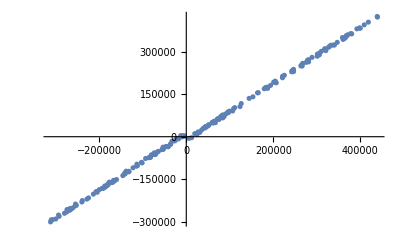

11

```mathematica
Table[
xlabel=label⟦1⟧;
ylabel=label⟦2⟧;
otherId=Delete[Range[Length[xstr]],{{xid[xlabel]},{xid[ylabel]}}];
positionEall=Position[type,"E"]//Flatten;
positionE=Select[positionEall,(Abs[mLs⟦#,otherId⟧-centralmodel⟦otherId⟧]//Max)<10^-6&];
pointE=Table[{mLs⟦pos,xid[xlabel]⟧,mLs⟦pos,xid[ylabel]⟧},{pos,positionE}];
(*plotE=plotsamples[pointE,RGBColor["#2ECC71"]];*)
Table[posOutput=pos;massfromλ[mLs⟦pos⟧,xmins⟦pos⟧//canonicalize]//massMatrix//Re//Eigenvalues,{pos,positionE}]//ListPlot(*[#,PlotRange->All]&*)
,{label,labelPairs⟦2;;2⟧}
]
```

```mathematica
pos=positionE⟦20⟧
xmins⟦pos⟧
mLs⟦pos⟧

{mLs⟦pos⟧,xstr}ᵀ
Table[mLs⟦pos⟧⟦xid⟦label⟧⟧,{label,{"a3","r1","r2","r3"}}]
massfromλ[mLs⟦pos⟧,xmins⟦pos⟧//canonicalize]//massMatrix(*//Re//Eigenvalues*)
Clear[pos]
```

330

{-1.1278,-3.2659,1.2088×10^-9,-1.46602×10^-9,-2.85292,6.86773×10^-9,-2.45745×10^-9,-1.57029×10^-8,1.80364×10^-9,3.17168,0.914135,0.102235,14.4561,-8.69135,-2.77381}

{5.,2.,9.,1.,0.,1.2,0.,1.,0.2,3.,0.,0.5,-2.2555,9.98865,0.,0.,0.}

{{5.,m1q},{2.,m2q},{9.,m3q},{1.,L1},{0.,L2},{1.2,L3},{0.,L4},{1.,r1},{0.2,r2},{3.,r3},{0.,r4},{0.5,a1},{-2.2555,a2},{9.98865,a3},{0.,b1},{0.,b2},{0.,b3}}

{9.98865,1.,0.2,3.}

{{-196574.,0.},{0.,-204826.}}

```mathematica
pos=420;
badDueToA[xmins⟦pos⟧]
xmins⟦pos⟧
xmins⟦pos⟧//canonicalize
(*massfromλ[mLs⟦pos⟧,xmins⟦pos⟧//canonicalize]*)
Clear[pos]
```

True

{-4.06228×10^-9,-1.82851×10^-8,-2.44815×10^-9,1.11768×10^-9,1.36563×10^-8,0.222358,0.649808,-1.89896,0.627919,1.99136,-0.6753,-2.75704,0.0284232,0.23356,0.438696}

494{4.06228×10^-9,1.82851×10^-8,1.36563×10^-8,1.11768×10^-9,-2.44815×10^-9,1.89896,0.649808,0.222358,6.9111,1.99136,-0.6753,-2.75704,3.17002,0.23356,0.438696}

{4.06228×10^-9,1.82851×10^-8,1.36563×10^-8,1.11768×10^-9,-2.44815×10^-9,1.89896,0.649808,0.222358,6.9111,1.99136,-0.6753,-2.75704,3.17002,0.23356,0.438696}

```mathematica
positionE//Length
```

184

## For m11m22 plots

```mathematica
xstr={"m1q","m2q","m3q",
"L1","L2","L3","L4",
"r1","r2","r3","r4",
"a1","a2","a3",
"b1","b2","b3"};
xid=Association[Table[xstr⟦i⟧->i,{i,xstr//Length}]];

(*centralmodel=1.0{0.5,0.2,9.0,
1.0,0.0,1.2,0.0,
0.2,0.2,0.2,0.2,
0.3,0.3,0.3,
0,0,0};*)
centralmodel=1.0{0.5,0.2,9.0,
1.0,0.0,1.2,0.0,
0.0,0.2,0.0,0.0,
0.3,0.3,0.3,
0,0,0};

xlist=1.0Subdivide[-4π,4π,39];
ylist=1.0Subdivide[-4π,4π,39];
labelPairs={{"r1","r3"}(*,{"r2","r3"}*)};

mLs={};
Table[
mLs=Join[mLs,
Table[model0=centralmodel;
model0⟦xid⟦label⟦1⟧⟧⟧=x;
model0⟦xid⟦label⟦2⟧⟧⟧=y;
model0
,{x,xlist},{y,ylist}]//Flatten[#,1]&
];
,{label,labelPairs}];
Print[{"mLs size",mLs//Dimensions}];
```

{mLs size,{1600,17}}

```mathematica
(*do not run them again!!!*)
nkernal=2;
If[Mod[Length[mLs],nkernal]==0,Print["OK"],Interrupt[]];
mLss=Partition[mLs,Length[mLs]/nkernal];
Table[Export[NotebookDirectory[]<>"scan-mass-data/input"<>ToString[i]<>".h5",{"mLs"-> mLss⟦i⟧}],{i,Length[mLss]}];
```

OK

```mathematica
(*************)
(*************)

(**run python:*)

command=Table[" py compute-mass.py "<>ToString[i]<>" & ",{i,1,nkernal}]//StringJoin

(*copy the result as "plain text"*)
(*************)
(*running time, ~20min*)
```

py compute-mass.py 1 &  py compute-mass.py 2 &

```mathematica
(*import python result*)
zeroFields={};
mLs={};
xmins={};
Vmins={};
seeds={};
mLnBFB={};

Table[
datapath=NotebookDirectory[]<>"scan-mass-data/result"<>ToString[i]<>".h5";
If[FileExistsQ[datapath],
zeroFields=Join[zeroFields,Import[datapath,"zerofields"]];
mLs=Join[mLs,Import[datapath,"m_L"]];
xmins=Join[xmins,Import[datapath,"x_min"]];
Vmins=Join[Vmins,Import[datapath,"V_min"]];
seeds=Join[seeds,Import[datapath,"seed"]];
mLnBFB=Join[mLnBFB,Import[datapath,"m_L_nBFB"]];
,
Print["not exist:"<>datapath];
];

,{i,nkernal(*{""}*)}];

Print[Length[Vmins]]
Dynamic[ishow]
```

700

```mathematica
same[x1_,x2_,ϵ_:10^-4]:=Abs[(Abs[x1]-Abs[x2])]<ϵ

badDueToA[xmin_]:=same[Table[xmin⟦j⟧,{j,1,2}]//Abs//Max,0];
badDueToB[xmin_]:=same[Table[xmin⟦j⟧,{j,3,8}]//Abs//Max,0];
badDueToC[xmin_]:=Not[same[det2[xmin]//Abs//Max,0]];
(*badDueToD[xmin_]:=And[same[xmin⟦3⟧,xmin⟦6⟧],same[xmin⟦4⟧,xmin⟦7⟧],same[xmin⟦5⟧,xmin⟦8⟧]];*)
badDueToD[xmin_]:=same[xmin⟦3⟧^2+2 xmin⟦4⟧^2+xmin⟦5⟧^2,xmin⟦6⟧^2+2 xmin⟦7⟧^2+xmin⟦8⟧^2];
goodE[xmin_]:=Or[same[xmin⟦1⟧,xmin⟦2⟧,10^-2],same[xmin⟦3⟧xmin⟦5⟧,0]&&same[xmin⟦4⟧,0]&&same[xmin⟦6⟧xmin⟦8⟧,0]&&same[xmin⟦7⟧,0]];

type=Table[0,{i,Length[zeroFields]}];
Do[
ishow=i;
If[badDueToA[xmins⟦i⟧],
type⟦i⟧="A";Continue[]
];
If[badDueToB[xmins⟦i⟧],
type⟦i⟧="B";Continue[]
];
If[badDueToC[xmins⟦i⟧],
type⟦i⟧="C";Continue[]
];
If[badDueToD[xmins⟦i⟧],
type⟦i⟧="D";Continue[]
];

If[goodE[xmins⟦i⟧],
type⟦i⟧="E";Continue[]
];

type⟦i⟧="X:unknown";


,{i,Length[zeroFields]}];

tallyList=type//Tally

Print[SortBy[%,First],
Length[seeds]
]
(*EandAll={Select[tallyList,#⟦1⟧=="E"&]⟦1,2⟧,Length[seeds]}
1.0EandAll⟦1⟧/EandAll⟦2⟧*)
```

{{D,576},{E,100},{C,24}}

{{C,24},{D,576},{E,100}}700

```mathematica
(**********************)
(*preparing for plots *)
(**********************)

δx=xlist⟦2⟧-xlist⟦1⟧;
δy=ylist⟦2⟧-ylist⟦1⟧;
plotgrid[xlist0_,ylist0_]:=Module[{xlist,ylist},

xlist=Append[xlist0-δx/2,xlist0⟦-1⟧+δx/2];

ylist=Append[ylist0-δy/2,ylist0⟦-1⟧+δy/2];
gridx=Table[Line[{{x,Min[ylist]},{x,Max[ylist]}}],{x,xlist}];
gridy=Table[Line[{{Min[xlist],y},{Max[xlist],y}}],{y,ylist}];
Graphics[{Gray,gridx,gridy}]
]
plotsamples[points_,color_]:=Graphics[{color,Table[Rectangle[point-{δx/2,δy/2},point+{δx/2,δy/2}],{point,points}]}]
```

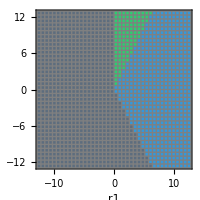

```mathematica
type2=type;
(*Do[type2⟦i⟧="E",{i,{130}}];
Do[type2⟦i⟧="E",{i,{426,447,422,420}}];
*)

labelαβ={"a1"->"α_1","a2"->"α_2","a3"->"α_3","b1"->"β_1","b2"->"β_2","b3"->"β_3"};
plots=Table[
xlabel=label⟦1⟧;
ylabel=label⟦2⟧;
otherId=Delete[Range[Length[xstr]],{{xid[xlabel]},{xid[ylabel]}}];
positionE=Position[type2,"E"]//Flatten;
positionE=Select[positionE,(Abs[mLs⟦#,otherId⟧-centralmodel⟦otherId⟧]//Max)<10^-6&];
pointE=Table[{mLs⟦pos,xid[xlabel]⟧,mLs⟦pos,xid[ylabel]⟧},{pos,positionE}];
plotE=plotsamples[pointE,RGBColor["#2ECC71"]];
positionA=Position[type2,_?(MemberQ[{"A","B","C","D"},#]&)]//Flatten;
positionA=Select[positionA,(Abs[mLs⟦#,otherId⟧-centralmodel⟦otherId⟧]//Max)<10^-6&];
pointA=Table[{mLs⟦pos,xid[xlabel]⟧,mLs⟦pos,xid[ylabel]⟧},{pos,positionA}];
plotA=plotsamples[pointA,RGBColor["#3498DB"]];

mLnBFB0=Select[mLnBFB,(Abs[#⟦otherId⟧-centralmodel⟦otherId⟧]//Max)<10^-6&];

pointnBFB=Table[{mLnBFB0⟦pos,xid[xlabel]⟧,mLnBFB0⟦pos,xid[ylabel]⟧},{pos,Length[mLnBFB0]}];
plotnBFB=plotsamples[pointnBFB,RGBColor["#5D6D7E"]];

plot=Show[{plotE,plotA,plotnBFB,plotgrid[xlist,ylist]},PlotRange->{4π{-1,1},4π{-1,1}},
(*PlotRangeClipping->True,*)
PlotRangePadding->1.2{1,1},
Frame->True,Axes->False,ImageSize->200,FrameLabel->({xlabel,ylabel}/.labelαβ),AspectRatio->1];
(*Export["D:\\Dropbox\\mywork\\LR-scalar\\LR-V\\fig\\"<>xlabel<>ylabel<>".pdf",plot];*)
plot
,{label,labelPairs}
]
```

### corresponding mass distributions

```mathematica
massfromλ[λ_(*potential para*),xmin_(*xmin*)]:=(*normalized v scale to 246GeV*)Module[{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3,(**)
m1q,m2q,m3q,L1,L2,L3,L4,r1,r2,r3,r4,a1,a2,a3,b1,b2,b3,(**)
vevRep,
other
},
{m1q,m2q,m3q,L1,L2,L3,L4,r1,r2,r3,r4,a1,a2,a3,b1,b2,b3}=λ;
{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}=canonicalize[xmin];


vevRep={(*Print[{f1,g1}];*)θL->f1-g1(*Warning: what if g1 are nonzero*),α->t2,vL->x1,vR->y1,myk1->k1,myk2->k2};

{"M11"->(r3-2 r1)vR^2+a3/2 (k1^2-k2^2),
"M22"->(4r2)vR^2+a3/2 (k1^2-k2^2),
"246GeV"->√(k1^2+k2^2)(*246.0/(√2)=173.xxx*)}/.vevRep]
```

```mathematica
maxabs[x_]:=Max[Abs[x]];

iσ2Transform[x_]:=Module[{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3},{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}=x;
{k2,k1,-x3,-x2,-x1,-y3,-y2,-y1,t2+0,f3,f2,f1,g3,g2,g1}
]

parityTransform[x_]:=Module[{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3},{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}=x;
{k1,k2,y1,y2,y3,x1,x2,x3,-t2,g1,g2,g3,f1,f2,f3}
]



canonicalize[xmin_]:=Module[{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3,(**)
exchange123,temp},
{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}=xmin;
If[maxabs[{x1,x2,x3}]>maxabs[{y1,y2,y3}],
(*exchange123={x1,x2,x3};{x1,x2,x3}={y1,y2,y3};{y1,y2,y3}=exchange123;
t2=-t2;*)
{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}=parityTransform[xmin]
];
(*If[Abs[x1]<Abs[x3],temp=x1;x1=x3;x3=temp];
If[Abs[y1]<Abs[y3],temp=y1;y1=y3;y3=temp];*)
If[Abs[y1]<Abs[y3],{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}=iσ2Transform[{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}]
];


If[x1<0,x1=-x1;f1=f1+π];
If[y1<0,y1=-y1;g1=g1+π];
If[k1<0,k1=-k1;t2=t2+π];
If[k2<0,k2=-k2;t2=t2+π];
(*If[same[Vatx[mλ,xmin],
Vatx[mλ,xmin//canonicalize]],Interrupt[]]*)
If[Or[k1<0,k2<0,x1<0,y1<0,Abs[x2]>0.1,Abs[x3]>0.1,Abs[y2]>0.1,Abs[y3]>0.1],Print[posOutput,{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}];(*Interrupt[]*)];
{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}
]
```

```mathematica
chargedMasses[rule_]:=(*x^2*)((*x->*)(246(*GeV*))/("246GeV"))^2{"M11","M22"}/.rule
```

```mathematica
(*plotsamples[pointE,RGBColor["#2ECC71"]]*)
```

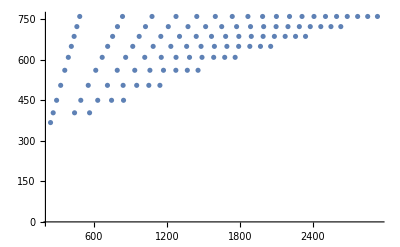

```mathematica
Table[
xlabel=label⟦1⟧;
ylabel=label⟦2⟧;
otherId=Delete[Range[Length[xstr]],{{xid[xlabel]},{xid[ylabel]}}];
positionEall=Position[type,"E"]//Flatten;
positionE=Select[positionEall,(Abs[mLs⟦#,otherId⟧-centralmodel⟦otherId⟧]//Max)<10^-6&];
pointE=Table[{mLs⟦pos,xid[xlabel]⟧,mLs⟦pos,xid[ylabel]⟧},{pos,positionE}];
(*plotE=plotsamples[pointE,RGBColor["#2ECC71"]];*)
plot=Table[posOutput=pos;massfromλ[mLs⟦pos⟧,xmins⟦pos⟧//canonicalize]//chargedMasses//Sqrt,{pos,positionE}]//ListPlot[#,PlotRange->All]&
,{label,labelPairs⟦1;;1⟧}
]
```

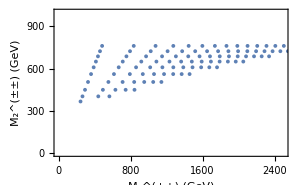

```mathematica
plot=Show[plot,PlotRange->{{0,2500},{0,1000}},Frame->True,Axes->False,FrameLabel->{"M_1^(±±) (GeV)","M_2^(±±) (GeV)"},ImageSize->300]
```

```mathematica
Export["D:\\Dropbox\\mywork\\LR-scalar\\LR-V\\fig\\M1M2.pdf",plot]
```

D:\Dropbox\mywork\LR-scalar\LR-V\fig\M1M2.pdf

## Function

```mathematica
det2[x_]:=Module[{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3},
{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}=x;Abs[{-ⅇ^(2 ⅈ f2) x2^2-ⅇ^(ⅈ f1+ⅈ f3) x1 x3,-ⅇ^(2 ⅈ g2) y2^2-ⅇ^(ⅈ g1+ⅈ g3) y1 y3}]
]

minimize[c_,min′rndseed_:0,fix_:{}]:=Module[{m1q,m2q,m3q,L1,L2,L3,L4,r1,r2,r3,r4,a1,a2,a3,b1,b2,b3},{m1q,m2q,m3q,L1,L2,L3,L4,r1,r2,r3,r4,a1,a2,a3,b1,b2,b3}=c;

variables={k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3};
If[Length[fix]>0,Do[variables=DeleteCases[variables,var];,{var,fix⟦All,1⟧}] ];

NMinimize[1/4 (k1^4 L1+k2^4 L1+2 k2^2 (-m1q+a3 (x1^2+x2^2+y1^2+y2^2)+a1 (x1^2+2 x2^2+x3^2+y1^2+2 y2^2+y3^2))+2 k1^2 (k2^2 (L1+2 L3)-m1q+a3 (x2^2+x3^2+y2^2+y3^2)+a1 (x1^2+2 x2^2+x3^2+y1^2+2 y2^2+y3^2))+4 (4 r2 x2^4+4 r2 x1^2 x3^2+r3 x1^2 y1^2+2 r3 x2^2 y1^2+r3 x3^2 y1^2+2 r3 x1^2 y2^2+4 r3 x2^2 y2^2+2 r3 x3^2 y2^2+4 r2 y2^4+(r3 (x1^2+2 x2^2+x3^2)+4 r2 y1^2) y3^2-m3q (x1^2+2 x2^2+x3^2+y1^2+2 y2^2+y3^2)+r1 ((x1^2+2 x2^2+x3^2)^2+(y1^2+2 y2^2+y3^2)^2)))+8 r2 x1 x2^2 x3 Cos[f1-2 f2+f3]+b2 k1^2 x1 y1 Cos[f1-g1]+8 r4 x2^2 y2^2 Cos[2 f2-2 g2]+8 r4 x1 x3 y2^2 Cos[f1+f3-2 g2]+b1 k1^2 x2 y2 Cos[f2-g2]+b1 k2^2 x2 y2 Cos[f2-g2]+b3 k1^2 x3 y3 Cos[f3-g3]+8 r4 x2^2 y1 y3 Cos[2 f2-g1-g3]+8 r4 x1 x3 y1 y3 Cos[f1+f3-g1-g3]+8 r2 y1 y2^2 y3 Cos[g1-2 g2+g3]+b3 k2^2 x1 y1 Cos[f1-g1-2 t2]+b1 k1 k2 x1 y1 Cos[f1-g1-t2]+2 b3 k1 k2 x2 y2 Cos[f2-g2-t2]+k1^3 k2 L4 Cos[t2]+k1 k2^3 L4 Cos[t2]-2 k1 k2 m2q Cos[t2]+2 a2 k1 k2 x1^2 Cos[t2]+4 a2 k1 k2 x2^2 Cos[t2]+2 a2 k1 k2 x3^2 Cos[t2]+2 a2 k1 k2 y1^2 Cos[t2]+4 a2 k1 k2 y2^2 Cos[t2]+2 a2 k1 k2 y3^2 Cos[t2]+2 k1^2 k2^2 L2 Cos[2 t2]+2 b2 k1 k2 x2 y2 Cos[f2-g2+t2]+b1 k1 k2 x3 y3 Cos[f3-g3+t2]+b2 k2^2 x3 y3 Cos[f3-g3+2 t2]/.fix
,variables,Method->{Automatic,RandomSeed->min′rndseed}]//Quiet
]
Vatx[c_,x_]:=Module[{m1q,m2q,m3q,L1,L2,L3,L4,r1,r2,r3,r4,a1,a2,a3,b1,b2,b3,
(**)
k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3},{m1q,m2q,m3q,L1,L2,L3,L4,r1,r2,r3,r4,a1,a2,a3,b1,b2,b3}=c;

{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}=x;

1/4 (k1^4 L1+k2^4 L1+2 k2^2 (-m1q+a3 (x1^2+x2^2+y1^2+y2^2)+a1 (x1^2+2 x2^2+x3^2+y1^2+2 y2^2+y3^2))+2 k1^2 (k2^2 (L1+2 L3)-m1q+a3 (x2^2+x3^2+y2^2+y3^2)+a1 (x1^2+2 x2^2+x3^2+y1^2+2 y2^2+y3^2))+4 (4 r2 x2^4+4 r2 x1^2 x3^2+r3 x1^2 y1^2+2 r3 x2^2 y1^2+r3 x3^2 y1^2+2 r3 x1^2 y2^2+4 r3 x2^2 y2^2+2 r3 x3^2 y2^2+4 r2 y2^4+(r3 (x1^2+2 x2^2+x3^2)+4 r2 y1^2) y3^2-m3q (x1^2+2 x2^2+x3^2+y1^2+2 y2^2+y3^2)+r1 ((x1^2+2 x2^2+x3^2)^2+(y1^2+2 y2^2+y3^2)^2)))+8 r2 x1 x2^2 x3 Cos[f1-2 f2+f3]+b2 k1^2 x1 y1 Cos[f1-g1]+8 r4 x2^2 y2^2 Cos[2 f2-2 g2]+8 r4 x1 x3 y2^2 Cos[f1+f3-2 g2]+b1 k1^2 x2 y2 Cos[f2-g2]+b1 k2^2 x2 y2 Cos[f2-g2]+b3 k1^2 x3 y3 Cos[f3-g3]+8 r4 x2^2 y1 y3 Cos[2 f2-g1-g3]+8 r4 x1 x3 y1 y3 Cos[f1+f3-g1-g3]+8 r2 y1 y2^2 y3 Cos[g1-2 g2+g3]+b3 k2^2 x1 y1 Cos[f1-g1-2 t2]+b1 k1 k2 x1 y1 Cos[f1-g1-t2]+2 b3 k1 k2 x2 y2 Cos[f2-g2-t2]+k1^3 k2 L4 Cos[t2]+k1 k2^3 L4 Cos[t2]-2 k1 k2 m2q Cos[t2]+2 a2 k1 k2 x1^2 Cos[t2]+4 a2 k1 k2 x2^2 Cos[t2]+2 a2 k1 k2 x3^2 Cos[t2]+2 a2 k1 k2 y1^2 Cos[t2]+4 a2 k1 k2 y2^2 Cos[t2]+2 a2 k1 k2 y3^2 Cos[t2]+2 k1^2 k2^2 L2 Cos[2 t2]+2 b2 k1 k2 x2 y2 Cos[f2-g2+t2]+b1 k1 k2 x3 y3 Cos[f3-g3+t2]+b2 k2^2 x3 y3 Cos[f3-g3+2 t2]

]
```